```mathematica
Clear["Global`*"]
```

```mathematica
kb = 1.38 10^(-16);
mp=1.67 10^(-24);
Msun=1.989 10^33;
G=6.67 10^(-8);
cmperau=1.5 10^13;
```

```mathematica
Tdisk[r_, T0_, betaT_]:=T0 r^(-betaT);
Sigmadisk[r_, Sigma0_, betaS_]:=Sigma0 r^(-betaS);
cdisk[r_, T0_, betaT_, mu_]:=Sqrt[kb Tdisk[r, T0, betaT ] / (mu mp)];
vth[r_, T0_, betaT_, mu_]:=Sqrt[8/Pi] cdisk[r, T0, betaT, mu];
Omegak[r_, Mstar_]:=Sqrt[G Mstar / (r cmperau)^3];
Hdisk[r_, T0_, betaT_, mu_, Mstar_]:=cdisk[r, T0, betaT, mu] / Omegak[r, Mstar];
rhodisk[r_, Sigma0_, betaS_, T0_, betaT_, mu_, Mstar_]:=Sigmadisk[r, Sigma0, betaS] / (Sqrt[2 Pi] Hdisk[r, T0, betaT, mu, Mstar]);
lambdamfp[r_, Sigma0_, betaS_, T0_, betaT_, mu_, Mstar_, sigma_]:=1/(Sqrt[2] sigma (rhodisk[r, Sigma0, betaS, T0, betaT, mu, Mstar] / (mu mp)));
eta[r_, T0_, betaT_, mu_, Mstar_, betaS_]:=cdisk[r, T0, betaT, mu]^2/(2 (Omegak[r, Mstar] r cmperau)^2);
ts[r_, s_, rhos_, T0_, betaT_, mu_, Sigma0_, betaS_, Mstar_, sigma_]:=rhos s /(rhodisk[r, Sigma0, betaS, T0, betaT, mu, Mstar] vth[r, T0, betaT, mu]);
taus[r_, s_, rhos_, T0_, betaT_, mu_, Sigma0_, betaS_, Mstar_, sigma_]:= ts[r, s, rhos, T0,  betaT, mu, Sigma0, betaS, Mstar, sigma] Omegak[r, Mstar];
tr[r_, s_, rhos_, T0_, betaT_, mu_, Sigma0_, betaS_, Mstar_, sigma_] :=(1+(taus[r, s, rhos, T0,  betaT, mu, Sigma0, betaS, Mstar, sigma])^2)/taus[r, s, rhos, T0,  betaT, mu, Sigma0, betaS, Mstar, sigma] / (2 eta[r, T0, betaT, mu, Mstar, betaS] Omegak[r, Mstar]);
rdot[r_, s_, rhos_, T0_,  betaT_, mu_, Sigma0_, betaS_, Mstar_, sigma_]:=-(r cmperau) / tr[r, s, rhos, T0,  betaT, mu, Sigma0, betaS, Mstar, sigma];
```

```mathematica
N[rdot[1., 0.1, 3, 120, 3/7, 2.35, 2200, 1, Msun, 2E-15]]
```

-0.30392

```mathematica
N[eta[1., 120, 3/7, 2.35, Msun, 1]]
```

0.000238548

```mathematica
N[cdisk[1., 120, 1, 2.35]]
```

64958.8

```mathematica
Tdisk[1, 120, 3/7]
```

120

```mathematica
sigma=2E-15;
s=1;
rhos=3;
T0=120;
betaT=3./7;
mu=2.35;
Sigma0=2200;
betaS=1.;
Mstar=Msun;
```

```mathematica
Mdot[r_, s_, rhos_, T0_,  betaT_, mu_, Sigma0_, betaS_, Mstar_, sigma_]:= -2 Pi (r cmperau ) rdot[r, s, rhos, T0,  betaT, mu, Sigma0, betaS, Mstar, sigma] Sigmadisk[r, Sigma0, betaS] 0.01 ;
```

```mathematica
x=Simplify[r/.Solve[D[Mdot[r, s, rhos, T0,  betaT, mu, Sigma0, betaS, Mstar, sigma], r]==0, r]][[1]]
```

-501.482

```mathematica
Mdot[1., 1, 3, 120, 3/7, 2.35, 2200, 1, Msun, 2E-15]
```

6.30161×10^15

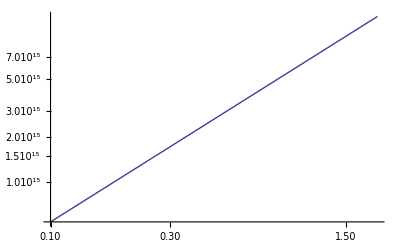

```mathematica
LogLogPlot[Mdot[r, 1, 3, 120, 3/7, 2.35, 2200, 1, Msun, sigma], {r, 0.1, 2}]
```